# Find Solution of System of Equations

## Q1. x’[t]+y[t]=sin(t), y’ + x=cos(t)

```mathematica
sol1=DSolve[{x'[t]+y[t]==Sin[t],y'[t]+x[t]==Cos[t]},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2]-1/4 (1+ⅇ^(-2 t)) (-1+ⅇ^(2 t)) Sin[t]+1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (1+ⅇ^(2 t)) Sin[t],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]-1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t))^2 Sin[t]+1/4 (1+ⅇ^(-2 t)) (1+ⅇ^(2 t)) Sin[t]}}

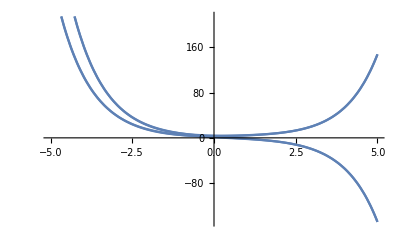

```mathematica
Plot[{x[t],y[t]}/.sol1/.{C[1]->{1,2},C[2]->{3,4}},{t,-5,5}]
```

## Q2. x’-7x+y=0, y’-2x+5 y = 0

```mathematica
sol2=DSolve[{x'[t]-7 x[t]+y[t]==0,y'[t]-2 x[t]+5 y[t]==0},{x[t],y[t]},t]
```

{{x[t]→1/34 ⅇ^(t-√34 t) (17-3 √34+17 ⅇ^(2 √34 t)+3 √34 ⅇ^(2 √34 t)) C[1]-(ⅇ^(t-√34 t) (-1+ⅇ^(2 √34 t)) C[2])/(2 √34),y[t]→(ⅇ^(t-√34 t) (-1+ⅇ^(2 √34 t)) C[1])/(√34)-1/34 ⅇ^(t-√34 t) (-17-3 √34-17 ⅇ^(2 √34 t)+3 √34 ⅇ^(2 √34 t)) C[2]}}

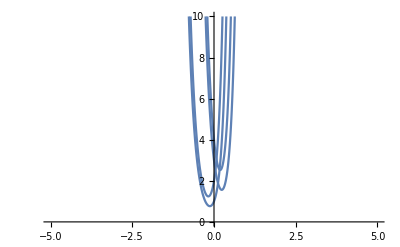

```mathematica
Plot[{x[t],y[t]}/.sol2/.{C[1]->{1,2},C[2]->{3,4}},{t,-5,5},PlotRange->{0,10}]
```

## Q3. x’-e^t+Tan(t)=0, y’+tan(t)-e^t=0

```mathematica
sol3=DSolve[{x'[t]-Exp[t]+Tan[t]==0,y'[t]+Tan[t]-Exp[t]==0},{x[t],y[t]},t]
```

{{x[t]→ⅇ^t+C[1]+Log[Cos[t]],y[t]→ⅇ^t+C[2]+Log[Cos[t]]}}

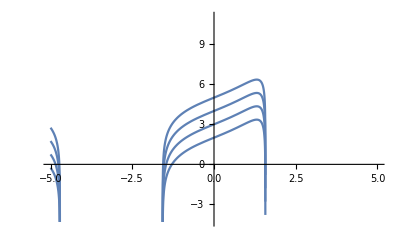

```mathematica
Plot[{x[t],y[t]}/.sol3/.{C[1]->{1,2},C[2]->{3,4}},{t,-5,5}]
```

## Q4. x’-x e^t + 2 y + 3 z=0, y’+2y-z=0, z’+z=0

```mathematica
sol4=DSolve[{x'[t]-x[t]*Exp[t]+2*y[t]+3*z[t]==0,y'[t]+2*y[t]-z[t]==0,z'[t]+z[t]==0},{x[t],y[t],z[t]},t]//Simplify
```

{{x[t]→ⅇ^(ⅇ^t) C[1]+ⅇ^(-2 t) C[2]-ⅇ^-t (C[2]-5 C[3])-ⅇ^(ⅇ^t) (C[2]-5 C[3]) ExpIntegralEi[-ⅇ^t],y[t]→ⅇ^(-2 t) (C[2]+ⅇ^t C[3]),z[t]→ⅇ^-t C[3]}}

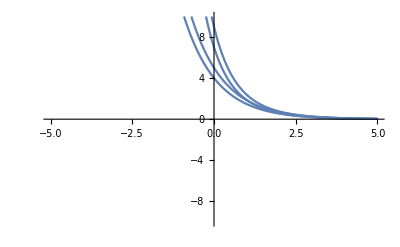

```mathematica
Plot[{x[t],y[t],z[t]}/.sol4/.{C[1]->{2,3},C[2]->{3,4},C[3]->{4,5}},{t,-5,5},PlotRange->{-10,10}]
```

## Q5. x’’’+y=0, y’’’-6+x=0; x[0]=0, y[0]=0

```mathematica
sol5=DSolve[{x'''[t]+y[t]==0,y'''[t]-6+x[t]==0,x[0]==0,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→1/6 ⅇ^-t (-6+12 ⅇ^t-6 ⅇ^(2 t)-C[2]+ⅇ^(2 t) C[2]+C[3]+ⅇ^(2 t) C[3]-C[5]-ⅇ^(2 t) C[5]+C[6]-ⅇ^(2 t) C[6]-12 ⅇ^(t/2) Cos[(√3 t)/2]-12 ⅇ^(3 t/2) Cos[(√3 t)/2]-ⅇ^(t/2) C[2] Cos[(√3 t)/2]+ⅇ^(3 t/2) C[2] Cos[(√3 t)/2]-ⅇ^(t/2) C[3] Cos[(√3 t)/2]-ⅇ^(3 t/2) C[3] Cos[(√3 t)/2]+ⅇ^(t/2) C[5] Cos[(√3 t)/2]+ⅇ^(3 t/2) C[5] Cos[(√3 t)/2]+ⅇ^(t/2) C[6] Cos[(√3 t)/2]-ⅇ^(3 t/2) C[6] Cos[(√3 t)/2]+24 ⅇ^t Cos[(√3 t)/2]^2+√3 ⅇ^(t/2) C[2] Sin[(√3 t)/2]+√3 ⅇ^(3 t/2) C[2] Sin[(√3 t)/2]-√3 ⅇ^(t/2) C[3] Sin[(√3 t)/2]+√3 ⅇ^(3 t/2) C[3] Sin[(√3 t)/2]-√3 ⅇ^(t/2) C[5] Sin[(√3 t)/2]+√3 ⅇ^(3 t/2) C[5] Sin[(√3 t)/2]+√3 ⅇ^(t/2) C[6] Sin[(√3 t)/2]+√3 ⅇ^(3 t/2) C[6] Sin[(√3 t)/2]+24 ⅇ^t Sin[(√3 t)/2]^2),y[t]→-1/6 ⅇ^-t (6-6 ⅇ^(2 t)+C[2]+ⅇ^(2 t) C[2]-C[3]+ⅇ^(2 t) C[3]+C[5]-ⅇ^(2 t) C[5]-C[6]-ⅇ^(2 t) C[6]-12 ⅇ^(t/2) Cos[(√3 t)/2]+12 ⅇ^(3 t/2) Cos[(√3 t)/2]-ⅇ^(t/2) C[2] Cos[(√3 t)/2]-ⅇ^(3 t/2) C[2] Cos[(√3 t)/2]-ⅇ^(t/2) C[3] Cos[(√3 t)/2]+ⅇ^(3 t/2) C[3] Cos[(√3 t)/2]+ⅇ^(t/2) C[5] Cos[(√3 t)/2]-ⅇ^(3 t/2) C[5] Cos[(√3 t)/2]+ⅇ^(t/2) C[6] Cos[(√3 t)/2]+ⅇ^(3 t/2) C[6] Cos[(√3 t)/2]+√3 ⅇ^(t/2) C[2] Sin[(√3 t)/2]-√3 ⅇ^(3 t/2) C[2] Sin[(√3 t)/2]-√3 ⅇ^(t/2) C[3] Sin[(√3 t)/2]-√3 ⅇ^(3 t/2) C[3] Sin[(√3 t)/2]-√3 ⅇ^(t/2) C[5] Sin[(√3 t)/2]-√3 ⅇ^(3 t/2) C[5] Sin[(√3 t)/2]+√3 ⅇ^(t/2) C[6] Sin[(√3 t)/2]-√3 ⅇ^(3 t/2) C[6] Sin[(√3 t)/2])}}

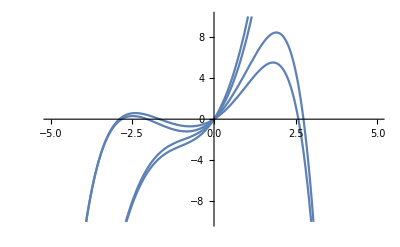

```mathematica
Plot[{x[t],y[t]}/.sol5/.{C[2]->{2,3},C[3]->{3,4},C[5]->{4,5},C[6]->{6,7}},{t,-5,5},PlotRange->{-10,10}]
```